```mathematica
a=NDSolve[{y'[x]==-(Cos[y[x]]/(x+2))+ 0.3*y[x]*y[x],y[0]==1},y,{x,0,3}]
```

{{y→InterpolatingFunction[…]}}

NDSolve::dvnoarg: The function y appears with no arguments.

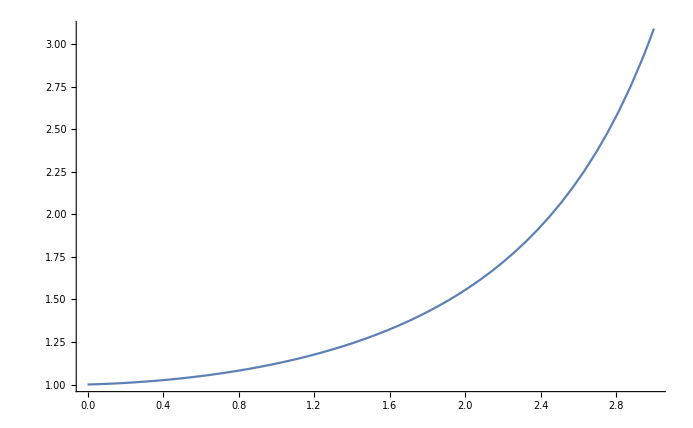

```mathematica
Plot[Evaluate[y[x]/.a],{x,0,3},PlotRange->All]
```